```mathematica
(* get the Schwarzian derivative of f *)
schwarzianDerivative[f_]:=Module[{},

d1=Derivative[0,1][N[f]];
d2=Derivative[0,2][N[f]];
d3=Derivative[0,3][N[f]];

Sf[r_,x_]:=Re[ComplexExpand[d3[r,x]/d1[r,x]-3/2*(d2[r,x]/d1[r,x])^2]];
Return[Sf]
];
```

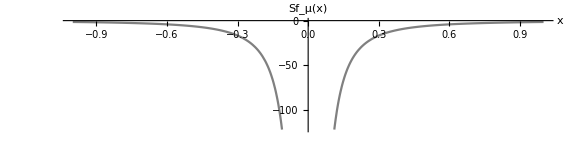

```mathematica
Plot[schwarzianDerivative[1-#1*#2^2&][1,x],{x,-1,1},AxesLabel->{x,"Sf_μ(x)"},ImageSize->Large,PlotStyle->Gray,AspectRatio->1/4]
```